## Householder Functions

```mathematica
(* Plot Householder set corresponding to matrix polynomials p and b on window [xl,xr]x[yl,yr], with the number of initial sample points equal to pts. *)
housePlot[p_,b_,n_,rho_,xl_,xr_,yl_,yr_,pts_]:=
RegionPlot[If[MatrixRank[b[x+I*y]]<n,True,Norm[LinearSolve[b[x+I*y],p[x+I*y]-b[x+I*y]],rho]≥1],{x,xl,xr},{y,yl,yr},PlotPoints->pts,MaxRecursion->0,PlotStyle->LightBlue,PlotTheme->"Scientific"];
```

```mathematica
(* Plot Weighted Gershgorin set corresponding to matrix polynomials p and b on window [xl,xr]x[yl,yr] and norm induced by d, with the number of initial sample points equal to pts. *)
wGershPlot[p_,b_,d_,n_,xl_,xr_,yl_,yr_,pts_]:=
RegionPlot[If[MatrixRank[b[x+I*y]]<n,True,Norm[LinearSolve[b[x+I*y].d,(p[x+I*y]-b[x+I*y]).d],Infinity]≥1],{x,xl,xr},{y,yl,yr},PlotPoints->pts,MaxRecursion->0,PlotStyle->LightBlue,PlotTheme->"Scientific"];
```

```mathematica
(* Computes the eigenvalues of matrix polynomial p by forming companion pencil stored in a and b and then using Eigenvalues routine to compute the eigenvalues of the pencil (a,b). *)
polyEig[p_]:=Module[{n,m,coeff,a,b},
n=Dimensions[p[z]][[1]];
m=Max[Table[Length[CoefficientList[p[z][[i,j]],z]],{i,1,n},{j,1,n}]]-1;
coeff=Coefficient[p[z],z,0];
If[m==1,Eigenvalues[N[-1*coeff]],
For[k=1,k<m,k++,
coeff=Join[coeff,Coefficient[p[z],z,k],2];
];
a=Join[Join[ConstantArray[0,{n*(m-1),n}],IdentityMatrix[n*(m-1)],2],-coeff,1];
b=Join[Join[IdentityMatrix[n*(m-1)],ConstantArray[0,{n*(m-1),n}],2],Join[ConstantArray[0,{n,n*(m-1)}],Coefficient[p[z],z,m],2],1];
Eigenvalues[{N[a],N[b]}]]];
```

```mathematica
(* Complex list plot of the eigenvalues of matrix polynomial p. *)
eigPlot[p_,c_]:=ListPlot[polyEig[p]/.{Complex[x_,y_]->{x,y},x_Real->{x,0}},PlotStyle->Directive[c,PointSize[Small]],PlotTheme->"Scientific"];
```

```mathematica
(* Forms the tridiagonal part of the matrix polynomial p. *)
triDiag[p_]:=Module[{n,b},
n=Dimensions[p[z]][[1]];
b=ConstantArray[0,{n,n}];
For[i=1,i≤n,i++,
For[j=Max[i-1,1],j≤Min[i+1,n],j++,
b[[i,j]]=p[z][[i,j]];
];
];
b];
```

```mathematica
(* Create random perturbation matrix polynomial *)
randPert[n_,m_,w_,eps_,rho_]:=Module[{coeff,a},
coeff={};
For[k=0,k<=m,k++,
a=RandomReal[{-1,1},{n,n}]+I*RandomReal[{-1,1},{n,n}];
a=a/Norm[a,rho];
a=a*(eps*w[[k+1]]);
coeff=Append[coeff,a];
];
Sum[z^(k-1)*coeff[[k]],{k,1,m+1}]
];
```

## Graph Laplacian

```mathematica
lap={{{5,-1,-1,-1,-1,-1},{0,3,-1,0,-1,-1},{0,0,2,0,-1,-1},{0,-1,-1,4,-1,-1},{0,0,0,0,1,-1},{0,0,0,0,0,0}},
{{5,-1,-1,-1,-1,-1},{0,3,0,-1,-1,-1},{-1,0,4,-1,-1,-1},{0,0,0,2,-1,-1},{0,0,0,0,1,-1},{0,0,0,0,0,0}},
{{3,-1,0,0,-1,-1},{0,2,-1,-1,0,0},{0,-1,1,0,0,0},{-1,0,0,2,0,-1},{0,0,0,-1,1,0},{-1,-1,-1,0,-1,4}},
{{3,-1,-1,-1,0,0},{0,1,-1,0,0,0},{0,0,0,0,0,0},{0,0,0,2,-1,-1},{0,0,0,0,1,-1},{0,0,0,0,0,0}}
};
```

```mathematica
a=lap[[1]];
q=RandomReal[{-1,1},{6,6}];
q[[All,1]]={1,1,1,1,1,1};
{q,r}=QRDecomposition[q];
q=Transpose[q];
q=q[[All,2;;6]];
l=Transpose[q].a.q;
Eigenvalues[l]
Eigenvalues[Transpose[l]]
Eigenvalues[l+Transpose[l]]
```

{5.,4.,3.,2.,1.}

{5.,4.,3.,2.,1.}

{10.3269,8.1474,6.,3.8526,1.67311}

```mathematica
Norm[a]
```

√30

### Dominance Graph

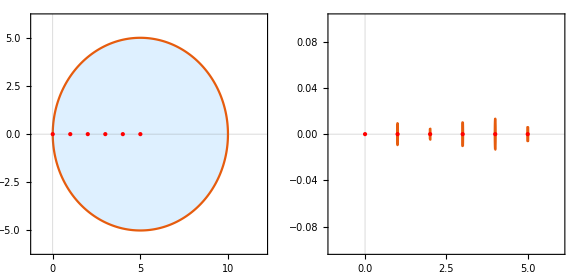

```mathematica
a=lap[[1]];
n=Dimensions[a][[1]];
m=1;
p[z_]=IdentityMatrix[n]*z-a;
d[z_]=DiagonalMatrix[Diagonal[p[z]]];
w=Table[Norm[Coefficient[p[z],z,k],Infinity],{k,0,m}];
pert[z_]=p[z]+randPert[n,m,w,0.001,Infinity];
e=eigPlot[p,Red];
f1=Show[housePlot[p,d,n,Infinity,-1.0,12.0,-6.0,6.0,250],e];
f2=Show[housePlot[pert,p,n,Infinity,-1.0,6.0,-0.1,0.1,250],e];
GraphicsRow[{f1,f2},ImageSize->Large]
```

### Dominance Graph + Perturbation

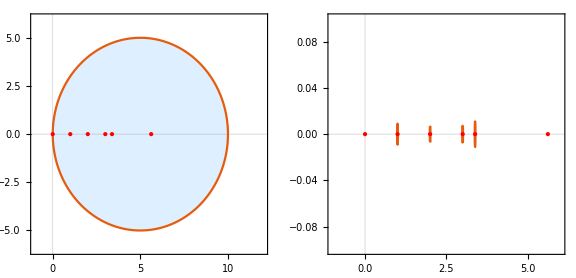

```mathematica
a=lap[[2]];
n=Dimensions[a][[1]];
m=1;
p[z_]=IdentityMatrix[n]*z-a;
d[z_]=DiagonalMatrix[Diagonal[p[z]]];
w=Table[Norm[Coefficient[p[z],z,k],Infinity],{k,0,m}];
pert[z_]=p[z]+randPert[n,m,w,0.001,Infinity];
e=eigPlot[p,Red];
f1=Show[housePlot[p,d,n,Infinity,-1.0,12.0,-6.0,6.0,250],e];
f2=Show[housePlot[pert,p,n,Infinity,-1.0,6.0,-0.1,0.1,250],e];
GraphicsRow[{f1,f2},ImageSize->Large]
```

### Perturbed Random Graph

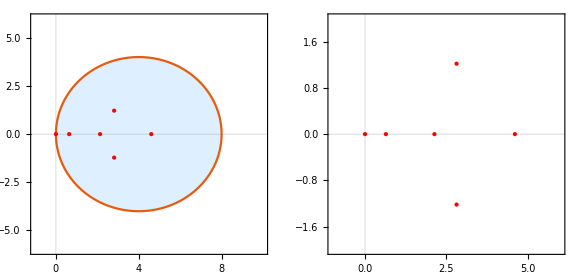

```mathematica
a=lap[[3]];
n=Dimensions[a][[1]];
m=1;
p[z_]=IdentityMatrix[n]*z-a;
d[z_]=DiagonalMatrix[Diagonal[p[z]]];
w=Table[Norm[Coefficient[p[z],z,k],Infinity],{k,0,m}];
pert[z_]=p[z]+randPert[n,m,w,0.001,Infinity];
e=eigPlot[p,Red];
f1=Show[housePlot[p,d,n,Infinity,-1.0,10.0,-6.0,6.0,250],e];
f2=Show[housePlot[pert,p,n,Infinity,-1.0,6.0,-2.0,2.0,250],e];
GraphicsRow[{f1,f2},ImageSize->Large]
```

### Nearly Disconnected

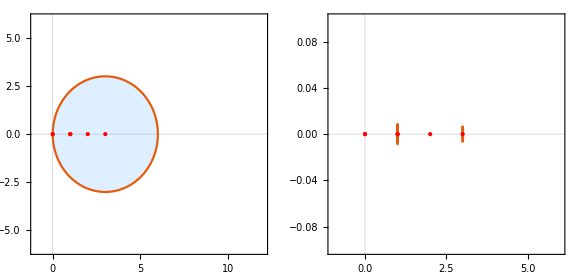

```mathematica
a=lap[[4]];
n=Dimensions[a][[1]];
m=1;
p[z_]=IdentityMatrix[n]*z-a;
d[z_]=DiagonalMatrix[Diagonal[p[z]]];
w=Table[Norm[Coefficient[p[z],z,k],Infinity],{k,0,m}];
pert[z_]=p[z]+randPert[n,m,w,0.001,Infinity];
e=eigPlot[p,Red];
f1=Show[housePlot[p,d,n,Infinity,-1.0,12.0,-6.0,6.0,250],e];
f2=Show[housePlot[pert,p,n,Infinity,-1.0,6.0,-0.1,0.1,250],e];
GraphicsRow[{f1,f2},ImageSize->Large]
```